```mathematica
INIT=2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120;
```

```mathematica
N[(2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120-2159062512564987644819455219116893945895958528152021228705752563807958532187555459247995)/443]
```

-9.82642×10^8

```mathematica
abacaxi=-Random[Integer,{Times[1.964179736959717,10^65],Times[9.964179736959717,10^77]}]
```

```mathematica
abacaxi=Random[Integer,{Times[1.964179736959717,10^8],Times[9.964179736959717,10^15]}]
```

4146712109788896

```mathematica
abacaxi=Random[Integer,{35093,95845}]
```

```mathematica
complexas=Table[i,{i,INIT,INIT+Times[Random[Integer,{523,685}],abacaxi],abacaxi}];Dimensions[complexas]
```

```mathematica
complexas=Table[i,{i,INIT,INIT+Times[Random[Integer,{223,485}],abacaxi],abacaxi}];Dimensions[complexas]
```

{472}

```mathematica
TAXA=0.7;
```

```mathematica
stepp=Table[s,{s,1,20,1}];
```

```mathematica
LEMBRAR QUE SE FOR 9 CICLOS, TIRA OS DOIS PRIMEIROS
```

```mathematica
TIRA SEMPRE PARES, contra ciclo duplo ?
```

```mathematica
TIRACICLO=0;
```

```mathematica
Condinit={{4,4,3,4,3,3,4,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4},{4,2,4,4,3,4,3,3,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,4,4,4,4,3,4,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4},{4,4,3,4,3,3,3,3,4,4,3,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,4},{4,3,3,4,2,3,4,3,4,4,3,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,3,3,4,4,4,4,4,4},{4,4,3,3,4,3,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{1,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}
```

{{4,4,3,4,3,3,4,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4},{4,2,4,4,3,4,3,3,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,4,4,4,4,3,4,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4},{4,4,3,4,3,3,3,3,4,4,3,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,4},{4,3,3,4,2,3,4,3,4,4,3,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,3,3,4,4,4,4,4,4},{4,4,3,3,4,3,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{1,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
Condnow={{4,3,4,4,4,4,4,4,3,4,3,4,3,4,4,4,4,4,3,4,4,4,4,4,0,4,3,4,3,4,4,4,4,3,2,4},{4,2,3,4,4,4,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,4},{4,1,3,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,4,3,4},{4,4,3,4,4,4,4,4,3,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,2,4,4,4,1,3,4},{4,2,2,4,3,4,4,3,4,3,3,4,4,4,4,4,4,3,4,4,4,4,4,4,0,4,3,4,4,3,4,4,4,3,3,4},{4,4,3,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,1,4,4,4,4,4,4,2,4,3,3,4},{4,4,3,3,4,4,3,4,3,3,4,4,4,3,4,4,4,4,3,4,4,3,4,4,0,4,3,4,4,3,4,4,3,3,3,3}}
```

{{4,3,4,4,4,4,4,4,3,4,3,4,3,4,4,4,4,4,3,4,4,4,4,4,0,4,3,4,3,4,4,4,4,3,2,4},{4,2,3,4,4,4,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,4},{4,1,3,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,4,3,4},{4,4,3,4,4,4,4,4,3,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,2,4,4,4,1,3,4},{4,2,2,4,3,4,4,3,4,3,3,4,4,4,4,4,4,3,4,4,4,4,4,4,0,4,3,4,4,3,4,4,4,3,3,4},{4,4,3,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,1,4,4,4,4,4,4,2,4,3,3,4},{4,4,3,3,4,4,3,4,3,3,4,4,4,3,4,4,4,4,3,4,4,3,4,4,0,4,3,4,4,3,4,4,3,3,3,3}}

```mathematica
gty=Table[rfy,{rfy,1,Max[stepp]+1,1}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
tgd=N[(Max[complexas]-Min[complexas])/abacaxi]
```

471.

```mathematica
numreg=Table[kik,{kik,1,Dimensions[complexas][[1]],1}];
```

```mathematica
dfh=Table[jo,{jo,1,Dimensions[Condinit][[1]],1}]
```

{1,2,3,4,5,6,7}

```mathematica
xyz=CellularAutomaton[{45234667543776875638879469696094904,5},Condinit[[1]],3];
```

```mathematica
7 conjuntos de 4 ciclos cada, sendo que o primeiro ciclo é Condinit[[x]]
```

```mathematica
dpp=CellularAutomaton[{45234667543776875638879469696094904,5},Condinit[[#]],Max[stepp]]&/@dfh;
```

```mathematica
Dimensions[xyz]
```

{4,167}

```mathematica
7 conjuntos de 4 ciclos cada, sendo que o primeiro ciclo é Condinit[[x]]
```

```mathematica
tabela[g_]:=CellularAutomaton[{g,5},Condinit[[#]],Max[stepp]]&/@dfh;
```

```mathematica
w=tabela/@complexas;
```

```mathematica
w[[regras]][[indicadores]] [[ciclos]]
```

## REMOÇÃO REGRAS PONTO FIXO

```mathematica
FIXO={1,2,3,4,5,6,7};
```

```mathematica
cost[dre_]:=Table[Total[Total[w[[dre]][[#]][[sara]]]&/@FIXO],{sara,1,Max[stepp]+1,1}]
```

```mathematica
SOMA EM CADA PASSO DE CADA UMA DAS REGRAS
```

```mathematica
zion=Table[ffg,{ffg,1,Dimensions[complexas][[1]],1}];
```

```mathematica
f5=cost/@zion;
```

```mathematica
rub=Table[f5[[#]][[isca]],{isca,1,Max[stepp]+1,1}]&/@numreg;
```

```mathematica
SE FOR TODA DE UMA COR, VALE ZERO, SENAO VALE 1
```

```mathematica
se[h_]:=If[rub[[h]][[#]]==Times[7,36],0,If[rub[[h]][[#]]==Times[Times[7,36],2],0,If[rub[[h]][[#]]==Times[Times[7,36],3],0,If[rub[[h]][[#]]==Times[Times[7,36],4],0,If[rub[[h]][[#]]==Times[Times[7,36],5],0,If[rub[[h]][[#]]==Times[Times[7,36],6],0,If[rub[[h]][[#]]==0,0,1]]]]]]]&/@gty
```

```mathematica
DETERMINA QUAIS CICLOS SAO BONS COM 1
```

```mathematica
laco=se/@numreg;
```

```mathematica
kirr=Drop[#,TIRACICLO]&/@laco;
```

## MELHOR REGRA E CICLO, MELHOR REGRA E CICLO, MELHOR REGRA E CICLO

```mathematica
caneta=Flatten[Position[kirr,Max[kirr]]];
```

```mathematica
mouse=Dimensions[caneta][[1]]
```

19784

### EXTRAIR AS REGRAS, IMPARES

```mathematica
mesa=Take[caneta,{1,mouse,2}];
```

### EXTRAI OS CICLOS PARES = CADEIRA

```mathematica
cadeira=Take[caneta,{2,mouse,2}];
```

```mathematica
love=Table[amor,{amor,1,Dimensions[cadeira][[1]],1}];
```

### REGRAS BOAS SEM HOMOGENEO = COPO

```mathematica
copo=complexas[[#]]&/@mesa;
```

### Lista de melhores regras e melhores ciclos para dar map NO AC. USAR CADEIRA E COPO

```mathematica
lixo={copo,cadeira};
```

```mathematica
relo[hora_]:=N[Count[(Condnow[[#]]-Last[CellularAutomaton[{copo[[hora]],5},Condinit[[#]],cadeira[[hora]]]])&/@dfh,0,2]]/Times[7,36]
```

### MAIORES ACERTOS DAS REGRAS BOAS

```mathematica
poo=relo/@love;
```

```mathematica
Max[poo]
```

0.746032

```mathematica
bxo=Table[ujy,{ujy,1,Dimensions[poo][[1]],1}];
```

### REGRAS BOAS QUE ACERTARAM MAIS QUE A TAXA ESTABELECIDA

```mathematica
alto=If[poo[[#]]>TAXA,1,0]&;
```

```mathematica
fork=alto/@bxo;
```

### JA SELECIONOU AS REGRAS BOAS, AGORA CRIA LISTA DE REGRAS BOAS COM MAIS DE 50% DE ACERTO PARA USAR NO ARRAY PLOT DIFERENÇA

```mathematica
fio=Flatten[Position[fork,1]];
```

```mathematica
gav=Table[eta,{eta,1,Dimensions[fio][[1]],1}];
```

### REGRAS COM MAIS DE TAXA% DE ACERTO

```mathematica
vent=copo[[fio[[#]]]]&/@gav;
```

```mathematica
papr=Table[palm,{palm,1,Dimensions[vent][[1]],1}];
```

## ACERTOS NAS MELHORES REGRAS BOAS E CICLOS - ARRAYPLOT DIFF E ACERTOS POO - VERDE MAIS QUE 75%

```mathematica
MELHORES REGRAS BOAS COM ACERTO ACIMA DA TAXA
```

```mathematica
melhoresregras=copo[[#]]&/@fio;
```

```mathematica
melhoresciclos=cadeira[[#]]&/@fio;
```

```mathematica
melhordetodos={melhoresregras,melhoresciclos};
```

```mathematica
doom=Table[quake,{quake,1,Dimensions[melhoresregras][[1]],1}];
```

```mathematica
bestofall=Flatten[Position[melhordetodos,Max[melhordetodos[[2]]]]][[2]]
```

7

```mathematica
bestofall=Flatten[Position[melhoresciclos,Max[melhoresciclos]]];
```

```mathematica
cadeira[[melhordetodos[[2]][[#]]]]&/@doom;
```

### MELHORES REGRAS BOAS COM ACERTO MAIOR DO QUE A TAXA

```mathematica
bestrules=copo[[#]]&/@fio;
```

```mathematica
cano=Table[pe,{pe,1,Dimensions[bestrules][[1]],1}];
```

### MELHORES ACERTOS NOS MELHORES CICLOS REGRAS BOAS COM ACERTO MAIOR DO QUE A TAXA

```mathematica
manga=poo[[#]]&/@fio;
```

### ACERTO MAXIMO DE TODAS REGRAS BOAS COM ACERTO MAIOR QUE A TAXA

```mathematica
BUSCAR AGORA  ENTRE AS MELHORES REGRAS A DE MENOR VARIANCIA
```

```mathematica
tvt[skg_]:=N[Mean[Variance[Last[CellularAutomaton[{bestrules[[skg]],5},Condinit[[#]],20]&/@dfh]]]]
```

```mathematica
adk=tvt/@cano;
```

```mathematica
tdd=N[Mean[Variance[Condnow]]]
```

0.25

```mathematica
keypt=tdd-adk[[#]]&/@cano;
```

```mathematica
keyttu=Abs[tdd-adk[[#]]]&/@cano;
```

```mathematica
SELECIONAR REGRAS DE VARIANCIA  PARECIDA
```

```mathematica
dwq=Cases[keyttu,x_/;(N[Mean[Variance[Condnow]]]-0)<x];
```

```mathematica
dwq=Cases[keyttu,x_/;(N[Mean[Variance[Condnow]]]-0.5)<x<(N[Mean[Variance[Condnow]]]+0.5)];
```

```mathematica
selectedrules=Flatten[Union[Position[keyttu,dwq[[#]]]&/@Table[pfdd,{pfdd,1,Dimensions[dwq][[1]],1}]]];
```

```mathematica
frep=melhoresregras[[selectedrules[[#]]]]&/@Table[pfdd,{pfdd,1,Dimensions[dwq][[1]],1}] ;
```

```mathematica
ptr=N[Total[Total[Condnow]]/Times[7,36]]-N[Total[Total[Condinit]]/Times[7,36]]
```

-0.103175

```mathematica
dtt[sapo_]:=N[Total[Total[Last[CellularAutomaton[{sapo,5},Condinit[[#]],20]]&/@FIXO]-Total[Condinit[[#]]&/@FIXO]]/Times[7,36]]
```

```mathematica
egg=dtt[#]&/@frep;
```

```mathematica
styp=Cases[egg,till_/;till<.05];
```

```mathematica
ovo=Union[Flatten[Position[egg,styp[[#]]]&/@Table[pgz,{pgz,1,Dimensions[styp][[1]],1}]]];
```

```mathematica
regraspot=frep[[#]]&/@ovo;
```

```mathematica
sjk=Union[Flatten[Position[bestrules,regraspot[[#]]]&/@Table[pasz,{pasz,1,Dimensions[regraspot][[1]],1}]]];
```

```mathematica
ACERTOMAX=Max[manga[[#]]&/@sjk]
```

0.72619

```mathematica
NAO PASSA DE 67% TEM QUE MANIPULAR COM QUEM INTERAGE -ORDEM ESTADO INICIAL - ORDENAR POR LOCAL E ORDENAR POR ORDEM CRESCENTE ou similaridade
```

```mathematica
MELHORREGRA=Union[bestrules[[Flatten[Position[manga,Max[manga[[#]]&/@sjk]]]]]]
```

{2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120,2159062512564987644819455219116893945895958528152021228705752563807958640001635003245416,2159062512564987644819455219116893945895958528152021228705752563807958839043816273112424,2159062512564987644819455219116893945895958528152021228705752563807958901244497919945864,2159062512564987644819455219116893945895958528152021228705752563807958930271482688468136,2159062512564987644819455219116893945895958528152021228705752563807959208101194044324168,2159062512564987644819455219116893945895958528152021228705752563807959506664465949124680,2159062512564987644819455219116893945895958528152021228705752563807959548131587047013640,2159062512564987644819455219116893945895958528152021228705752563807959556425011266591432,2159062512564987644819455219116893945895958528152021228705752563807959701559935109202792,2159062512564987644819455219116893945895958528152021228705752563807959817667874183291880,2159062512564987644819455219116893945895958528152021228705752563807960008416631233581096,2159062512564987644819455219116893945895958528152021228705752563807960095497585539147912,2159062512564987644819455219116893945895958528152021228705752563807960103791009758725704,2159062512564987644819455219116893945895958528152021228705752563807960149404842966403560,2159062512564987644819455219116893945895958528152021228705752563807960398207569553737320}

```mathematica
asa=Table[pasa,{pasa,1,Dimensions[MELHORREGRA][[1]],1}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
DISTÂNCIA EUCLIDIANA
```

```mathematica
ako=N[EuclideanDistance[Condinit[[#]],Condnow[[#]]]]&/@dfh
```

{5.74456,3.31662,4.24264,4.3589,5.,4.58258,6.55744}

```mathematica
ajop=N[EuclideanDistance[Condinit[[#]],Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],11]][[1]]]]&/@dfh
```

{3.,3.4641,2.,3.,4.,2.44949,10.4403}

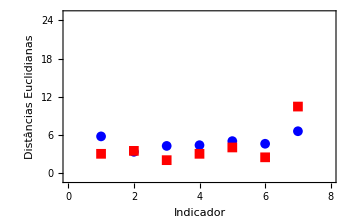

```mathematica
ListPlot[{ako, ajop},TicksStyle->Directive[Red,Bold],PlotRange->{{0,8},{-1,25}},Frame->True,ImageSize->350,FrameStyle->Directive[Black,Medium],FrameLabel->{"Indicador","Distâncias Euclidianas"},InterpolationOrder->3,PlotMarkers->{Automatic,Medium},PlotStyle->{ Blue,Red},Frame->True]
```

```mathematica
DISTÂNCIA EUCLIDIANA ENTRE INDIVÍDUOS
```

```mathematica
primeiro indivíduo
```

indivíduo primeiro

```mathematica
pessoas[foww_]:=Condinit[[#]][[foww]]&/@dfh
```

```mathematica
kgf=pessoas/@Table[i,{i,1,36}];
```

```mathematica
sal=N[EuclideanDistance[kgf[[1]],kgf[[#]]]]&/@Table[i,{i,2,36}];
```

```mathematica
pessoa2[foww_]:=Condnow[[#]][[foww]]&/@dfh
```

```mathematica
kgdd=pessoa2/@Table[i,{i,1,36}];
```

```mathematica
sal2=N[EuclideanDistance[kgdd[[1]],kgdd[[#]]]]&/@Table[i,{i,2,36}];
```

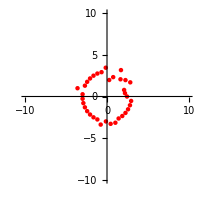
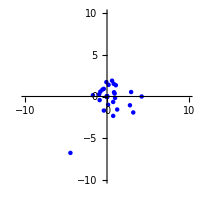

```mathematica
{ListPolarPlot[sal,PlotRange->10,PlotStyle->Directive[PointSize[0.016],Red],Mesh->All,ImageSize->200],ListPolarPlot[sal2,PlotRange->10,PlotStyle->Directive[PointSize[0.016],Blue],Mesh->All,ImageSize->200]}
```

```mathematica
NO MODELO
```

```mathematica
Manipulate[skl=Last[CellularAutomaton[{MELHORREGRA[[priss]],5},Condinit[[#]],ptf]]&/@dfh;pessoa3[foww_]:=skl[[#]][[foww]]&/@dfh;kgdd3=pessoa3/@Table[i,{i,1,36}];sal3=N[EuclideanDistance[kgdd3[[1]],kgdd3[[#]]]]&/@Table[i,{i,2,36}];{ListPolarPlot[sal,PlotRange->10,PlotStyle->Directive[PointSize[0.02],Red],Mesh->All,ImageSize->170],ListPolarPlot[sal2,PlotRange->10,PlotStyle->Directive[PointSize[0.02],Blue],Mesh->All,ImageSize->170],ListPolarPlot[sal3,PlotRange->10,PlotStyle->Directive[PointSize[0.02],Blue],Mesh->All,ImageSize->170]},{ptf,12,20,1},{priss,1,Dimensions[MELHORREGRA][[1]],1}]
```

```mathematica
3,16
```

```mathematica
MÉDIA
```

```mathematica
FFfc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Mean[Mean[Condinit]]],N[Mean[Mean[Condnow]]],N[Mean[Flatten[FFfc/@FIXO]]]}
```

{3.75794,3.65476,3.74603}

```mathematica
VARIANCIAS - consenso
```

```mathematica
vrc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Mean[Variance[Condinit]]],N[Mean[Variance[Condnow]]],N[Variance[Flatten[vrc/@FIXO]]]}
```

{0.169312,0.25,0.700183}

```mathematica
DESVIO PADRÃO
```

```mathematica
tfc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Mean[StandardDeviation[Condinit]]],N[Mean[StandardDeviation[Condnow]]],N[StandardDeviation[Flatten[tfc/@FIXO]]]}
```

{0.250852,0.375052,0.83677}

```mathematica
MEDIANA
```

```mathematica
Ftrfc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Median[Flatten[Condinit]]],N[Median[Flatten[Condnow]]],N[Median[Flatten[Ftrfc/@FIXO]]]}
```

{4.,4.,4.}

```mathematica
SKEWNESS
```

```mathematica
FtFfc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Skewness[Flatten[Condinit]]],N[Skewness[Flatten[Condnow]]],N[Skewness[Flatten[FtFfc/@FIXO]]]}
```

{-2.21834,-2.72005,-3.50195}

```mathematica
KURTOSIS
```

```mathematica
Ffc[tju_]:=Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[tju]],11]]
```

```mathematica
{N[Kurtosis[Flatten[Condinit]]],N[Kurtosis[Flatten[Condnow]]],N[Kurtosis[Flatten[Ffc/@FIXO]]]}
```

{8.03703,11.8201,14.562}

```mathematica
AUMENTO DE PERCEPCAO REAL
```

```mathematica
N[Total[Total[Condnow]-Total[Condinit]]/Times[7,36]]
```

-0.103175

```mathematica
AUMENTO DE PERCEPCAO MODELO
```

```mathematica
N[Mean[Mean[(Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],11]]-Condinit[[#]])&/@FIXO]]]
```

-0.0119048

### TAXAS DE ACERTO PARA A MELHOR REGRA EM 30 CICLOS

```mathematica
CICLOS DE CONSUMO - TAXAS DE ACERTO
```

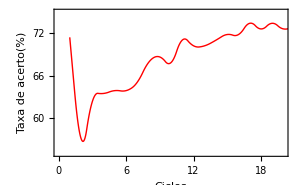

```mathematica
fada=Table[peter,{peter,0,20,1}];ist[jop_]:=Times[N[Count[(Condnow[[jop]]-Last[CellularAutomaton[{MELHORREGRA[[2]],5},Condinit[[jop]],#]]),0,2]]/Times[7,36],100]&/@fada;{ListLinePlot[Total[ist/@FIXO],InterpolationOrder->2,PlotStyle->{Red,Thick,PointSize[Medium]},TicksStyle->Directive[Red,Bold],PlotRange->{{0,20},{55,75}},Frame->True,FrameLabel->{"Ciclos","Taxa de acerto(%)"},ImageSize->300,FrameStyle->Directive[Black,Medium]]}
```

```mathematica
dissonancia cognitiva
```

```mathematica
GRÁFICO DE AUMENTO DE PERCEPÇÃO REAL e modelo
```

```mathematica
dhj=Total[((Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],11]]-Condinit[[#]])/7)&/@FIXO];
```

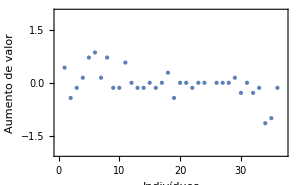
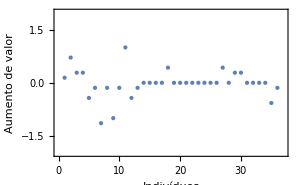

```mathematica
{ListPlot[(Total[Condnow]-Total[Condinit])/7,PlotStyle->PointSize[0.01],TicksStyle->Directive[Red,Bold],PlotRange->{{0,37},{-2,2}},Frame->True,FrameLabel->{"Indivíduos","Aumento de valor"},ImageSize->300,FrameStyle->Directive[Black,Medium]],ListPlot[dhj,PlotStyle->PointSize[0.01],TicksStyle->Directive[Red,Bold],PlotRange->{{0,37},{-2,2}},Frame->True,FrameLabel->{"Indivíduos","Aumento de valor"},FrameStyle->Directive[Black,Medium],ImageSize->300]}
```

```mathematica
TOTAL DOS VALORES DE CONDNOW E MODELO
```

```mathematica
Manipulate[{ListPlot[Total[Condinit]/13,PlotStyle->PointSize[0.01],TicksStyle->Directive[Red,Bold],PlotRange->{{0,37},{1,5}},Frame->True,FrameLabel->{"Indivíduos-Condinit","Aumento de valor"},ImageSize->250,FrameStyle->Directive[Black,Medium]]/.{0.->1,1.->2,2.->3,3.->4,4.->5},ListPlot[Total[Condnow]/7,PlotStyle->PointSize[0.01],TicksStyle->Directive[Red,Bold],PlotRange->{{0,37},{1,5}},Frame->True,FrameLabel->{"Indivíduos-Condnow","Aumento de valor"},ImageSize->250,FrameStyle->Directive[Black,Medium]]/.{0.->1,1.->2,2.->3,3.->4,4.->5},ListPlot[Total[Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],ciclosp]]&/@FIXO]/7,PlotStyle->PointSize[0.01],TicksStyle->Directive[Red,Bold],PlotRange->{{0,37},{1,5}},Frame->True,FrameLabel->{"Indivíduos-Modelo","Aumento de valor"},FrameStyle->Directive[Black,Medium],ImageSize->250]/.{0.->1,1.->2,2.->3,3.->4,4.->5},#},{ciclosp,0,40,1}]
```

```mathematica
GRÁFICO DE AUMENTO DE PERCEPÇÃO MODELO
```

```mathematica
TAXAS DE ACERTO NO RETICULADO
```

```mathematica
pt=Grid[Condnow[[#]]-Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],20]]&/@FIXO,Frame->All]
```

0 | -1 | 0 | 2 | 2 | 4 | 4 | 1 | -1 | 4 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -2 | 0
0 | -2 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | -3 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 2 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | -3 | -1 | 0
0 | -2 | 2 | 4 | 2 | 2 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0
0 | 1 | 1 | 4 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | -1 | -1 | 0
2 | 0 | -1 | -1 | 0 | 0 | -1 | 1 | -1 | 3 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -4 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 3 | 0

```mathematica
CORES USADAS PARA O AJUSTE DO MODELO
```

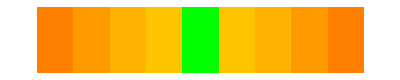

```mathematica
ArrayPlot[{{-4,-3,-2,-1,0,1,2,3,4}},ColorRules->{-4->RGBColor[1,0.5,0],-3->RGBColor[1,0.6,0],-2->RGBColor[1,0.7,0],-1->RGBColor[1,0.77,0],0->RGBColor[0,1,0],1->RGBColor[1,0.77,0],2->RGBColor[1,0.7,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.5,0]}]
```

```mathematica
AJUSTE DO MODELO
```

```mathematica
Manipulate[ArrayPlot[(Condnow[[#]]-Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],gts]])&/@FIXO,ColorRules->{-6->RGBColor[1,0,0],-5->RGBColor[1,0.4,0],-4->RGBColor[1,0.5,0],-3->RGBColor[1,0.6,0],-2->RGBColor[1,0.7,0],-1->RGBColor[1,0.77,0],0->RGBColor[0,1,0],1->RGBColor[1,0.77,0],2->RGBColor[1,0.7,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.5,0],5->RGBColor[1,0.4,0],6->RGBColor[1,0,0]},ImageSize->400,Mesh->True],{gts,0,40,1}]
```

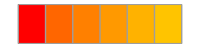

```mathematica
ArrayPlot[{{1,2,3,4,5,6}},Mesh->True,ColorRules->{1->RGBColor[1,0,0],2->RGBColor[1,0.4,0],3->RGBColor[1,0.5,0],4->RGBColor[1,0.6,0],5->RGBColor[1,0.7,0],6->RGBColor[1,0.77,0]}]
```

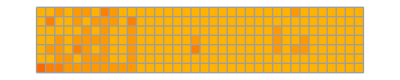

```mathematica
ArrayPlot[Condinit,ColorRules->{0->RGBColor[1,0,0],1->RGBColor[1,0.4,0],2->RGBColor[1,0.5,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.7,0],5->RGBColor[1,0.77,0]},ImageSize->400,Mesh->True]
```

```mathematica
JÁ DA PRA VER OS CLUSTERS DE CONSENSO - NOTAR A FORMAÇÃO DO CLUSTER NO AC À DIREITA HEHEHE
```

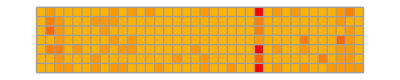

```mathematica
ArrayPlot[Condnow,ColorRules->{0->RGBColor[1,0,0],1->RGBColor[1,0.4,0],2->RGBColor[1,0.5,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.7,0],5->RGBColor[1,0.77,0]},ImageSize->400,Mesh->True]
```

```mathematica
Manipulate[{ArrayPlot[Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],plo]]&/@FIXO,ColorRules->{0->RGBColor[1,0,0],1->RGBColor[1,0.4,0],2->RGBColor[1,0.5,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.7,0],5->RGBColor[1,0.77,0]},ImageSize->400,Mesh->True],plo},{plo,0,40,1}]
```

```mathematica
3
```

```mathematica
EVOLUÇÃO DE CADA LINHA
```

```mathematica
Export["modelofinal.xls",Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],15]]&/@FIXO/.{0.->1,1.->2,2.->3,3.->4,4.->5}]
```

modelofinal.xls

```mathematica
TOTAL POR  INDICADOR
```

```mathematica
fun[stpp_]:=Total[Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[stpp]],#]]]&/@Table[psdd,{psdd,0,30,1}]
```

```mathematica
PREÇO NÃO MUDOU - LOGO MUDOU MENOS
```

```mathematica
Total[Condinit[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]
```

{137,136,140,135,132,138,129}

```mathematica
Total[Condnow[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]
```

{130,135,136,134,127,133,126}

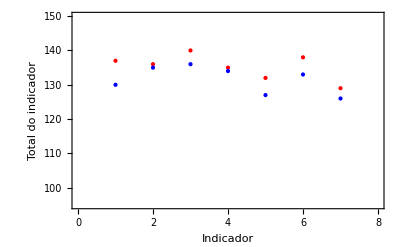
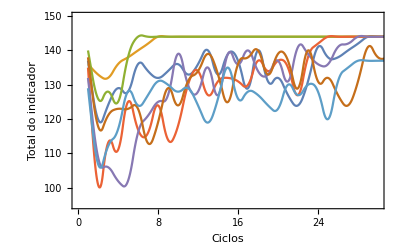

```mathematica
{ListPlot[{Total[Condinit[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}],Total[Condnow[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]},InterpolationOrder->2,Frame->True,FrameLabel->{"Indicador","Total do indicador"},ImageSize->400,PlotRange->{{0,8},{95,150}},PlotStyle->{{Red,Thick,PointSize[Medium]},{Blue,Thick,PointSize[Medium]}},FrameStyle->Directive[Black,Medium]],ListLinePlot[sfg=fun/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}],InterpolationOrder->2,PlotRange->{{0,30},{95,150}},Frame->True,FrameLabel->{"Ciclos","Total do indicador"},ImageSize->400,FrameStyle->Directive[Black,Medium]]}
```

```mathematica
MÉDIA TOTAL DOS INDICADORES NOS CICLOS- LIMIAR DE ADOÇÃO - DISSONÂNCIA COGNITIVA PÓS COMPRA !!!!!!!!!!!!!!
```

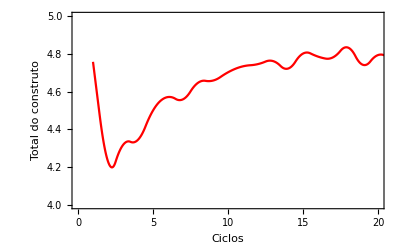

```mathematica
ListLinePlot[{(Total[fun/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]]+Times[7,36])/Times[7,36]},InterpolationOrder->2,PlotRange->{{0,20},{4,5}},Frame->True,FrameLabel->{"Ciclos","Total do construto"},FrameStyle->Directive[Black,Medium],PlotStyle->{Red,Thick,PointSize[Medium]}]
```

```mathematica
EVOLUÇÃO DA VARIÂNCIA PARA CADA INDICADOR
```

```mathematica
frr[stvv_]:=Variance[Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[stvv]],#]]]&/@Table[psdd,{psdd,1,40,1}]
```

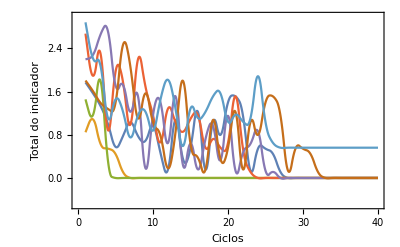
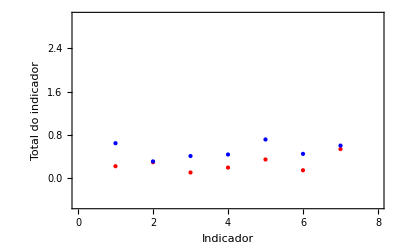

```mathematica
{ListLinePlot[frr/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}],InterpolationOrder->2,Frame->True,FrameLabel->{"Ciclos","Total do indicador"},PlotRange->{{0,40},{-.5,3}},ImageSize->400,TicksStyle->Directive[Black,20],FrameStyle->Directive[Black,Medium]],ListPlot[{Variance[Condinit[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}],Variance[Condnow[[#]]]&/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]},InterpolationOrder->2,Frame->True,FrameLabel->{"Indicador","Total do indicador"},ImageSize->400,PlotRange->{{0,8},{-.5,3}},PlotStyle->{{Red,Thick,PointSize[Medium]},{Blue,Thick,PointSize[Medium]}},FrameStyle->Directive[Black,Medium]]}
```

```mathematica
APOS O NONO CICLO ACHA A ESTABILIDADE / PESSOAS INCONSTANTES ATRATOR CICLICO / cada indicador tem um tempo de atingir estabilidade
```

```mathematica
O 4 TENDE A EXPANDIR A INSATISFAÇÃO, MAS QDO ENCONTRA O INDIVÍDUO LARANJA CLARO, EVOLUÇÃO DA INSATISFAÇÃO PARA DE PROPAGAR E SOME
```

```mathematica
Condinit
```

{{4,4,3,4,3,3,4,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4},{4,2,4,4,3,4,3,3,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,4,4,4,4,3,4,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4},{4,4,3,4,3,3,3,3,4,4,3,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,4},{4,3,3,4,2,3,4,3,4,4,3,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,3,3,4,4,4,4,4,4},{4,4,3,3,4,3,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{1,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
Manipulate[{ArrayPlot[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[indicador]],sstepss],ColorRules->{0->RGBColor[1,0,0],1->RGBColor[1,0.4,0],2->RGBColor[1,0.5,0],3->RGBColor[1,0.6,0],4->RGBColor[1,0.7,0],5->RGBColor[1,0.77,0]},ImageSize->400,Mesh->True],indicador},{sstepss,0,30,1},{indicador,1,7,1}]
```

```mathematica
TABELA DE TRANSICAO
```

```mathematica
q12=Reverse@Tuples[{0,1,2,3,4},3]
```

{{4,4,4},{4,4,3},{4,4,2},{4,4,1},{4,4,0},{4,3,4},{4,3,3},{4,3,2},{4,3,1},{4,3,0},{4,2,4},{4,2,3},{4,2,2},{4,2,1},{4,2,0},{4,1,4},{4,1,3},{4,1,2},{4,1,1},{4,1,0},{4,0,4},{4,0,3},{4,0,2},{4,0,1},{4,0,0},{3,4,4},{3,4,3},{3,4,2},{3,4,1},{3,4,0},{3,3,4},{3,3,3},{3,3,2},{3,3,1},{3,3,0},{3,2,4},{3,2,3},{3,2,2},{3,2,1},{3,2,0},{3,1,4},{3,1,3},{3,1,2},{3,1,1},{3,1,0},{3,0,4},{3,0,3},{3,0,2},{3,0,1},{3,0,0},{2,4,4},{2,4,3},{2,4,2},{2,4,1},{2,4,0},{2,3,4},{2,3,3},{2,3,2},{2,3,1},{2,3,0},{2,2,4},{2,2,3},{2,2,2},{2,2,1},{2,2,0},{2,1,4},{2,1,3},{2,1,2},{2,1,1},{2,1,0},{2,0,4},{2,0,3},{2,0,2},{2,0,1},{2,0,0},{1,4,4},{1,4,3},{1,4,2},{1,4,1},{1,4,0},{1,3,4},{1,3,3},{1,3,2},{1,3,1},{1,3,0},{1,2,4},{1,2,3},{1,2,2},{1,2,1},{1,2,0},{1,1,4},{1,1,3},{1,1,2},{1,1,1},{1,1,0},{1,0,4},{1,0,3},{1,0,2},{1,0,1},{1,0,0},{0,4,4},{0,4,3},{0,4,2},{0,4,1},{0,4,0},{0,3,4},{0,3,3},{0,3,2},{0,3,1},{0,3,0},{0,2,4},{0,2,3},{0,2,2},{0,2,1},{0,2,0},{0,1,4},{0,1,3},{0,1,2},{0,1,1},{0,1,0},{0,0,4},{0,0,3},{0,0,2},{0,0,1},{0,0,0}}

```mathematica
BEST OF ALL = 2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120
```

```mathematica
forest=RandomChoice[{1,1,0},{50,50}];
forest=ReplacePart[forest,RandomChoice[Position[forest,1]]->3];
```

```mathematica
out=CellularAutomaton[{MELHORREGRA[[1]],5},#,50]&/@forest
```

{{{1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,1,1,1},{1,0,1,3,1,1,1,0,1,3,1,0,1,3,1,0,1,3,1,1,1,1,0,1,4,1,3,1,0,1,3,0,0,4,4,1,4,0,4,4,0,4,4,0,4,4,1,3,1,1},{0,1,0,0,1,1,0,1,0,0,3,1,0,0,3,1,0,0,1,1,1,0,1,1,2,0,0,3,1,0,1,3,4,2,3,2,0,4,2,4,4,2,4,4,2,3,0,0,1,1},45,{4,3,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,1,0,3,1,0,2,3,3,0,2,3,3,1,0,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{2,4,0,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,0,1,3,4,3,4,4,4,3,4,0,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,0,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,0,3,0,2,4,4,0,4,2,4,0,0,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},49}
 |  |  |  |

```mathematica
out
```

{{{1,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,1,1,1},{1,0,1,3,1,1,1,0,1,3,1,0,1,3,1,0,1,3,1,1,1,1,0,1,4,1,3,1,0,1,3,0,0,4,4,1,4,0,4,4,0,4,4,0,4,4,1,3,1,1},{0,1,0,0,1,1,0,1,0,0,3,1,0,0,3,1,0,0,1,1,1,0,1,1,2,0,0,3,1,0,1,3,4,2,3,2,0,4,2,4,4,2,4,4,2,3,0,0,1,1},45,{4,3,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,0,1,0,3,1,0,2,3,3,0,2,3,3,1,0,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{2,4,0,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,0,1,3,4,3,4,4,4,3,4,0,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,0,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,0,3,0,2,4,4,0,4,2,4,0,0,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},49}
 |  |  |  |

```mathematica
Export["CA_test4.gif",MatrixPlot[#,ColorRules->{0->White,1->Red,2->Yellow,3->Orange,4->Green}]&/@Transpose[out]]
```

CA_test2.gif

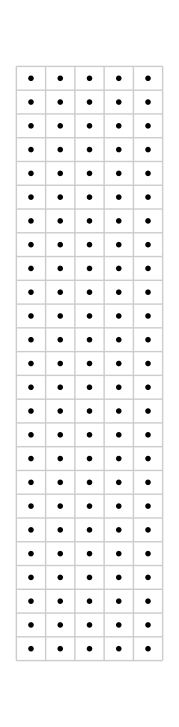

```mathematica
RulePlot[CellularAutomaton[{2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120,5}]]
```

```mathematica
uau12=IntegerDigits[MELHORREGRA[[1]],5,Dimensions[q12][[1]]]
```

{4,2,4,3,4,4,2,0,3,4,4,0,0,0,3,2,0,3,2,4,4,0,2,3,2,0,4,4,4,0,1,0,0,0,4,2,4,0,3,0,2,3,3,1,3,4,3,4,0,3,4,3,1,2,0,1,4,1,4,2,3,0,4,3,0,1,4,2,1,2,1,1,3,0,2,0,3,2,2,0,2,2,0,0,1,4,3,4,3,3,2,2,1,1,0,4,0,4,1,0,2,4,0,1,3,2,1,3,1,2,2,3,4,0,3,1,0,3,3,4,4,2,4,4,0}

```mathematica
ru12=Table[sal12,{sal12,1,Max[Dimensions[uau12][[1]]],1}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125}

```mathematica
tod12=ReplacePart[{0,0,0},uau12[[#]],2]&/@ru12
```

{{0,4,0},{0,2,0},{0,4,0},{0,3,0},{0,4,0},{0,4,0},{0,2,0},{0,0,0},{0,3,0},{0,4,0},{0,4,0},{0,0,0},{0,0,0},{0,0,0},{0,3,0},{0,2,0},{0,0,0},{0,3,0},{0,2,0},{0,4,0},{0,4,0},{0,0,0},{0,2,0},{0,3,0},{0,2,0},{0,0,0},{0,4,0},{0,4,0},{0,4,0},{0,0,0},{0,1,0},{0,0,0},{0,0,0},{0,0,0},{0,4,0},{0,2,0},{0,4,0},{0,0,0},{0,3,0},{0,0,0},{0,2,0},{0,3,0},{0,3,0},{0,1,0},{0,3,0},{0,4,0},{0,3,0},{0,4,0},{0,0,0},{0,3,0},{0,4,0},{0,3,0},{0,1,0},{0,2,0},{0,0,0},{0,1,0},{0,4,0},{0,1,0},{0,4,0},{0,2,0},{0,3,0},{0,0,0},{0,4,0},{0,3,0},{0,0,0},{0,1,0},{0,4,0},{0,2,0},{0,1,0},{0,2,0},{0,1,0},{0,1,0},{0,3,0},{0,0,0},{0,2,0},{0,0,0},{0,3,0},{0,2,0},{0,2,0},{0,0,0},{0,2,0},{0,2,0},{0,0,0},{0,0,0},{0,1,0},{0,4,0},{0,3,0},{0,4,0},{0,3,0},{0,3,0},{0,2,0},{0,2,0},{0,1,0},{0,1,0},{0,0,0},{0,4,0},{0,0,0},{0,4,0},{0,1,0},{0,0,0},{0,2,0},{0,4,0},{0,0,0},{0,1,0},{0,3,0},{0,2,0},{0,1,0},{0,3,0},{0,1,0},{0,2,0},{0,2,0},{0,3,0},{0,4,0},{0,0,0},{0,3,0},{0,1,0},{0,0,0},{0,3,0},{0,3,0},{0,4,0},{0,4,0},{0,2,0},{0,4,0},{0,4,0},{0,0,0}}

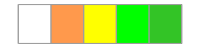

```mathematica
ArrayPlot[{{0,1,2,3,4}},Mesh->True,ColorRules->{0->White,1->RGBColor[1,0.6,0.3],2->Yellow,3->Green,4->RGBColor[0.2,0.77,0.15]},ImageSize->200]
```

```mathematica
SIGNIFICA QUE DEVEMOS CONTRARIAR O CLIENTE PARA FAZE-LO FELIZ ?????
```

```mathematica
asj=ArrayPlot[{q12[[#]],tod12[[#]]},Mesh->True,ImageSize->50,ColorRules->{0->White,1->RGBColor[1,0.6,0.3],2->Yellow,3->Green,4->RGBColor[0.2,0.77,0.15]}]&/@ru12
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DIFERENÇAS ENTRE CONDNOW E CONDINIT - MAIOR DE 0 E 1
```

```mathematica
Count[Flatten[Condinit],#]&/@{0,1,2,3,4}
```

{0,1,7,44,200}

```mathematica
Count[Flatten[Condnow],#]&/@{0,1,2,3,4}
```

{3,3,8,50,188}

```mathematica
jgu[bbb_]:=Count[Flatten[Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[bbb]],15]]],#]&/@{0,1,2,3,4}
```

```mathematica
Total[jgu/@{1,2,3,4,5,6,7}]
```

{11,4,7,3,227}

```mathematica
grapff[wrr_]:=With[{diffee = Condnow-Condinit
},{Count[Flatten[diffee],#]&/@{0,1,2,3,4}}]
```

```mathematica
grapff[1][[1]]
```

{180,26,3,1,0}

```mathematica
Total[{grapff[1][[1]][[1]],grapff[1][[1]][[2]]}]
```

206

```mathematica
TOTAL DE DIFERENÇAS 0 E 1
```

```mathematica
N[(grapff[1][[1]][[1]]+grapff[1][[1]][[2]])/Total[grapff[1][[1]]]]
```

0.980952

```mathematica
CONTAGEM DE DIFERENÇAS ENTRE O MODELO E CONDINIT - TB - MAIOR DE 0 E 1
```

```mathematica
graphixy[w_]:=With[{diffee = (Last[CellularAutomaton[{MELHORREGRA[[1]],5},Condinit[[#]],11]]-Condinit[[#]])&/@FIXO
},{Count[Flatten[diffee],#]&/@{0,1,2,3,4}}]
```

```mathematica
graphixy[1][[1]]
```

{191,32,6,0,0}

```mathematica
Total[{graphixy[1][[1]][[1]],graphixy[1][[1]][[2]]}]
```

223

```mathematica
TOTAL DE DIFERENÇAS 0 E 1
```

```mathematica
N[(graphixy[1][[1]][[1]]+graphixy[1][[1]][[2]])/Total[graphixy[1][[1]]]]
```

0.973799

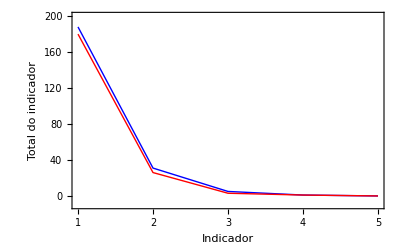

```mathematica
ListLinePlot[{graphixy[1][[1]],grapff[1][[1]]},PlotStyle->{Blue, Red},Frame->True,ImageSize->400,FrameLabel->{"Indicador","Total do indicador"},PlotRange->{{1,5},{-10,200}},FrameStyle->Directive[Black,Medium]]
```

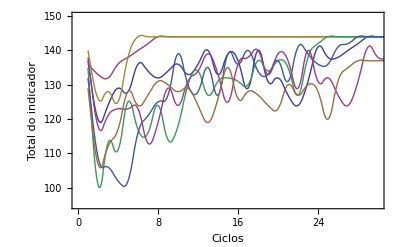

```mathematica
ListLinePlot[sfg=fun/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}],InterpolationOrder->2,PlotRange->{{0,30},{95,150}},Frame->True,FrameLabel->{"Ciclos","Total do indicador"},ImageSize->400,FrameStyle->Directive[Black,Medium]]
```

```mathematica
sfg=fun/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}]
```

{{137,120,124,129,128,136,134,132,134,136,133,136,140,133,139,137,129,140,131,132,127,124,131,141,138,138,140,142,144,144,144},{136,133,132,136,138,140,142,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144},{140,126,128,125,138,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144,144},{135,101,113,111,125,117,116,124,114,118,130,134,127,131,132,131,130,137,134,137,135,127,138,142,144,144,144,144,144,144,144},{132,109,106,102,102,116,121,125,127,139,130,128,135,127,139,136,140,134,133,137,131,141,139,136,136,141,142,144,144,144,144},{138,118,121,123,123,123,113,119,129,124,131,134,139,133,125,136,138,140,133,139,137,129,140,131,132,127,124,131,141,138,138},{129,107,112,117,128,124,127,131,130,128,129,124,119,126,135,126,128,127,124,123,130,127,130,128,120,131,135,137,137,137,137}}

```mathematica
CADA INDICADOR TEM UMA EVOLUÇÃO, QDO FICA RETO CONVERGIU PARA PONTO FIXO
```

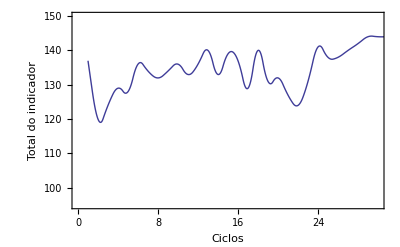
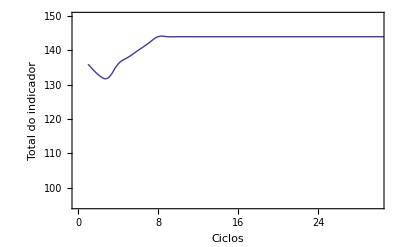
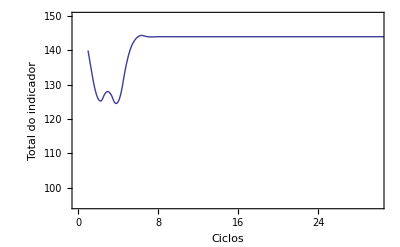
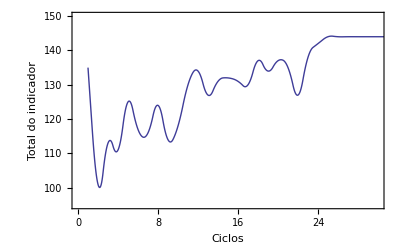
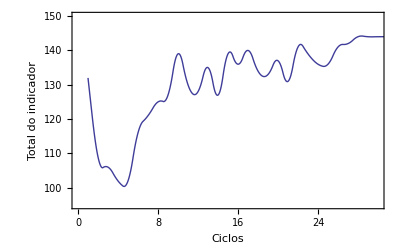
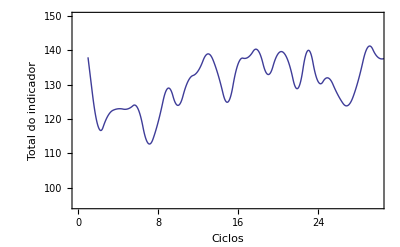
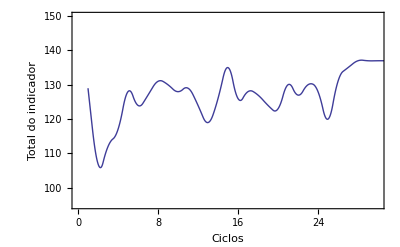

```mathematica
ss=ListLinePlot[(sfg=fun/@Table[psdd,{psdd,1,Dimensions[Condinit][[1]],1}])[[#]],InterpolationOrder->2,PlotRange->{{0,30},{95,150}},Frame->True,FrameLabel->{"Ciclos","Total do indicador"},ImageSize->400,FrameStyle->Directive[Black,Medium]]&/@{1,2,3,4,5,6,7}
```

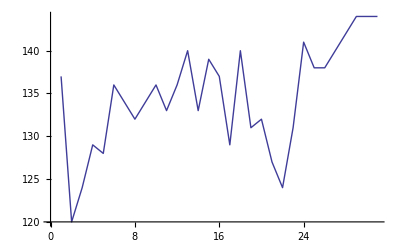

```mathematica
fvv=ListLinePlot[sfg[[1]]]
```

```mathematica
Sound[ListPlay[sfg[[1]],SampleRate->2896]]
```

-Graphics-

```mathematica
st=Flatten[Table[sfg,{100}]];Sound[ListPlay[st,SampleRate->2896]]
```

-Graphics-

```mathematica
st=Flatten[Table[sfg[[4]],{500}]];ListPlay[st,SampleRate->2896]
```

-Graphics-

```mathematica
Export["test.mid",{Flatten[Table[sfg,{100}]]}]
```

Export::nodta: {{137, 120, 124, 129, 128, 136, 134, 132, 134, 136, 133, 136, 140, 133, 139, 137, 129, 140, 131, 132, 127, 124, 131, 141, 138, 138, 140, 142, 144, 144, 144, 136, 133, 132, 136, 138, 140, 142, 144, 144, 144, 144, 144, 144, 144, 144, 144, 144, 144, 144, « 21650 »}} contains no data that can be exported to the "MIDI" format.

$Failed

```mathematica
RandomInteger[1,{10,200}]
```

{{0,0,1,0,0,1,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0,0,1,0,1,0,1,0,1,1,1,1,1,1,0,1,0,0,0,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,0,1,0,1,1,0,0,1,0,0,0,0,1,0,1,0,1,1,1,0,0,0,1,1,1,0,0,1,1,1,0,0,1,0,0,1,1,0,0,0,1,1,1,1,0,1,1,0,0,1,0,1,0,0,0,0,1,1,1,0,1,1,0,1,0,0,1,1,1,0,0,0,1,1,1,0,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0,0,1},{1,0,1,1,0,0,0,1,0,0,1,0,0,1,0,0,0,1,1,0,1,0,0,1,1,0,0,0,0,1,1,1,0,1,0,0,1,0,0,1,1,1,1,0,1,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,0,1,0,0,0,1,1,1,0,1,1,1,0,1,0,0,0,1,1,1,1,0,1,1,0,1,1,1,0,1,0,0,1,1,0,1,1,0,1,0,1,1,1,1,0,0,1,1,1,0,1,0,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,1,1,0,1,1,0,1,1,1,0,0,1,0,0,0,0,1,1,1,0,0,1,0,1,0,1,0,1,0,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,0,0,0,1,1,1,1,0,1,0},{1,1,1,0,0,0,0,1,0,1,1,0,0,1,0,0,1,0,1,0,1,0,0,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0,1,1,1,0,1,1,1,1,0,0,0,1,0,0,0,0,0,1,0,1,1,1,0,0,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,1,1,0,0,1,1,1,1,0,1,1,1,1,1,1,0,1,0,0,1,1,1,0,1,1,0,0,0,1,1,1,1,1,1,0,1,1,1,0,0,1,1,0,1,1,1,0,1,1,0,0,0,0,1,1,1,1,1},{0,0,0,1,0,0,1,1,1,1,1,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,0,1,1,1,0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,1,1,1,0,1,1,0,0,0,1,1,1,0,1,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,1,1,0,0,1,0,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,0,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1,1,1,1,0,1,0,1,1,0,0,0},{1,0,1,0,0,0,1,1,0,0,1,0,0,0,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0,1,1,0,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,0,0,0,0,1,1,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,0,1,1,0,1,0,1,0,0,0,0,1,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,0,1,1,1,1,0,1,1,0,0,1,1,1,0,1,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,0,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,0,0,1,0,0,0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,1,1,0,0,1,0,0,1,0,0,1,1,1,1,1,0,0,0,0,1,0,0,1,1,0,0,0,1,0},{0,1,0,0,1,1,1,1,1,0,0,1,0,0,0,0,0,1,0,1,1,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,0,0,1,1,0,1,0,0,1,1,1,0,0,0,0,1,1,1,0,1,1,0,1,0,0,0,0,1,1,1,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,1,0,0,1,1,0,0,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,0,0,1,1,1,1,1,0,1,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1,1,1},{0,0,0,1,1,1,0,0,1,0,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,1,1,1,1,1,0,1,0,0,0,0,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,0,0,1,1,1,1,1,0,1,0,0,1,0,1,0,0,1,1,0,1,0,0,0,1,0,0,0,1,0,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,0,1,1,0,1,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,1,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,0,0,1,0},{1,0,1,0,0,0,0,1,1,1,1,0,0,0,1,1,1,1,0,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,0,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,0,1,0,1,1,1,0,0,1,1,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1,1,1,0,1,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,0,1,1,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,0,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0,0,1},{1,1,1,1,1,0,0,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,0,1,0,0,1,1,1,0,1,0,1,0,1,0,1,1,1,0,0,0,0,1,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,0,1,1,1,0,1,1,1,1,0,1,0,0,1,0,1,0,0,0,1,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,1,1,0,0,1,1,1,0,1,1,1,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1,1,1,1,1,0,1,0},{0,1,0,1,1,1,1,0,1,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,1,1,1,0,1,1,1,1,0,0,0,0,1,0,0,1,1,1,0,1,1,1,1,1,0,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1,1,1,1,0,0,1,0,0,1,0,1,0,0,0,0,1,0,1,1,1,0,0,1,0,1,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,0,1,0,1,1,1,1,0,0}}

```mathematica
Condinit
```

{{4,4,3,4,3,3,4,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4},{4,2,4,4,3,4,3,3,3,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{4,4,4,4,4,3,4,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4},{4,4,3,4,3,3,3,3,4,4,3,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,3,4,4,3,4,4,4,4,4,4},{4,3,3,4,2,3,4,3,4,4,3,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,3,4,3,3,4,4,4,4,4,4},{4,4,3,3,4,3,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},{1,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}

```mathematica
RandomInteger[5,{1,200}]
```

{{5,2,3,2,0,2,0,1,1,4,1,5,0,1,5,5,0,3,4,4,2,0,1,0,0,1,3,0,5,5,3,2,4,4,2,3,3,5,5,1,0,1,4,2,0,4,2,1,3,5,2,1,4,0,0,1,0,1,2,2,0,4,5,2,0,2,4,5,1,1,5,0,2,5,5,1,3,3,2,4,1,0,1,4,3,2,1,3,1,1,1,5,5,5,1,2,4,0,0,2,1,3,3,5,2,1,5,3,3,4,3,2,5,1,0,0,2,4,3,3,4,0,2,0,2,5,5,2,4,2,5,2,5,4,1,3,3,2,0,3,2,5,0,2,5,3,3,5,3,1,3,4,0,0,1,4,0,5,3,5,4,5,0,4,5,4,4,3,5,3,0,3,3,5,2,3,4,0,4,0,4,2,0,1,5,1,0,2,3,3,1,4,2,0,4,1,4,2,2,0}}

```mathematica
ArrayPlot[Mean/@CellularAutomaton[{2159062512564987644819455219116893945895958528152021228705752563807958532187120148734120,5},RandomInteger[1,{1,200}][[0]],100]]
```

CellularAutomaton::initn: The initial condition specification List should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 4.

Mean::rectt: Rectangular array expected at position 1 in Mean[100].

CellularAutomaton::nspecnl: Rule specification 2159062512564987644819455219116893945895958528152021228705752563807958532187120148734125/2 should be an Integer, a List, a pure Boolean function, a String, or an Association.

ArrayPlot::mat: Argument CellularAutomaton[2159062512564987644819455219116893945895958528152021228705752563807958532187120148734125/2,Mean[List],Mean[100]] at position 1 is not a list of lists.

ArrayPlot[CellularAutomaton[2159062512564987644819455219116893945895958528152021228705752563807958532187120148734125/2,Mean[List],Mean[100]]]